## Figure 3: Distribution of review times at Econometrica and REStud

```mathematica
(*Set fpath below to the project directory.*)
fpath="/Users/erinhengel/Dropbox/Readability/draft";
SetDirectory[fpath];
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn = OpenSQLConnection[JDBC["SQLite", fpath<>"/0-data/fixed/read.db"]];
font="Avenir Light";
```

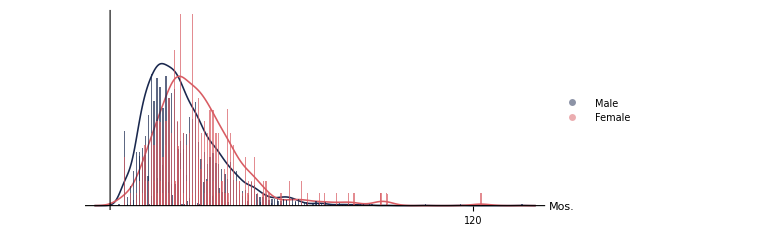

```mathematica
Clear[sql]
TimeHistogram[fname_,showLegend_,ticks_]:=Module[
{sql,data,male,female,opacity,blue,pink,legend,kernel,histogram,plot,name,fpath,legendFontColour,legendMaleColour,legendFemaleColour},
sql="SELECT (JULIANDAY(Accepted) - JULIANDAY(Received)) / 30 AS ReviewLength, AVG(Female) AS FemRatio FROM Article NATURAL JOIN (SELECT AuthorID, ArticleID, CASE WHEN Sex = 'Female' THEN 1 ELSE 0 END AS Female FROM AuthorCorr NATURAL JOIN Author) WHERE Received IS NOT NULL AND PubDate<'2016-01-01' AND (Journal='ECA' OR Journal='RES') AND Title NOT LIKE '%corrigendum%' AND Title NOT LIKE '%erratum%' AND Title NOT LIKE '%: a correction%' AND Title NOT LIKE '%: correction' GROUP BY ArticleID;";
data= SQLExecute[conn, sql];
male=Select[data,#⟦2⟧<0.5&]⟦All,1⟧;
female=Select[data,#⟦2⟧≥0.5&]⟦All,1⟧;
opacity=Opacity[0.7];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
{legendFontColour,legendMaleColour,legendFemaleColour}=If[TrueQ[showLegend],{Gray,blue,pink},{White,White,White}];
legend=PointLegend[{legendMaleColour,legendFemaleColour},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->30,
LabelStyle->{FontSize->36,FontColor->legendFontColour,FontFamily->font},
LegendMargins->5,
LegendLayout->"Row"
];
kernel=SmoothHistogram[{male,female},
PlotStyle->{
{blue,Thickness[0.002]},
{pink,Thickness[0.002]}
},
AxesOrigin->{-5,0},
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium],
Ticks->ticks,
TicksStyle->Directive[FontSize->28]
];
histogram=Histogram[{male,female},{0.1},"Probability",
ChartStyle->{
Directive[blue,opacity],
Directive[pink,opacity]},
ChartLegends->Placed[legend,{Right,Center}]
];
plot=Show[
{kernel,histogram},
PlotRange->All,
AxesLabel->{Style["Mos.",FontSize->28],None},
ImageSize->Full,
AspectRatio->0.4
];

name=SQLExecute[conn,"SELECT Name FROM JournalName WHERE Journal='ECA' OR Journal='RES';"];
Export[fname,plot];
Show[plot,ImageSize->Large]
];
TimeHistogram["0-images/generated/Figure-3.png",True,{{120},{0.1}}]
```